```mathematica
(* load jet3coords_checknew.nb *)
```

```mathematica
(* now do x2 grid *)
```

```mathematica
Clear[myhslope2,x2,ntheta]
theta2=Pi/2*(myhslope2*(2*x2-1)+(1-myhslope2)*(2*x2-1)^ntheta+1)
```

1/2 π (1+myhslope2 (-1+2 x2)+(1-myhslope2) (-1+2 x2)^ntheta)

```mathematica
extreme=Solve[D[theta2,x2]==0,x2]//.{x2->x2extreme}
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x2extreme→1/2 (1+(myhslope2/((-1+myhslope2) ntheta))^(1/(-1+ntheta)))}}

```mathematica
(* Require x2<=0 and x2>=1 *)
```

```mathematica
hslopelimit=Solve[0==x2extreme//.extreme[[1]],myhslope2]
myhslopelimit=hslopelimit[[1,1,2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{myhslope2→((-1)^ntheta ntheta)/(1+(-1)^ntheta ntheta)}}

((-1)^ntheta ntheta)/(1+(-1)^ntheta ntheta)

```mathematica
hslopelimit//.{ntheta->21.}
```

{{myhslope2→1.05}}

```mathematica
hslopelimit//.{ntheta->3}
```

{{myhslope2→3/2}}

```mathematica
(* This is largest myhslope2 can be for a given ntheta *)
```

```mathematica
N2=256
sx2=0
ex2=1
(* nthetai and nthetaf have to be odd integers *)
(*nthetai=21*)
nthetai=3
nthetaf=1
htheta=0.15
Qjet=1.3
r1jet=2.8
njet=0.3
r0jet=20
rsjet=80

rsjet2=5
r0jet2=2

r0jet3=150
rsjet3=20
nujet=3/4
sjet=2/nujet
alpha=1/sjet
```

256

0

1

3

1

0.15

1.3

2.8

0.3

20

80

5

2

150

20

3/4

8/3

3/8

```mathematica
(* arctan goes from ~0 at small distances to 1 at largest distances *)
```

```mathematica
0.5+1/Pi*(ArcTan[(r-rsjet)/r0jet])//.{ii->TS1}//.sol//.consts
```

1.

```mathematica
arctan=0.5+1/Pi*(ArcTan[(r-rsjet)/r0jet])//.sol//.consts;arctan2=0.5+1/Pi*(ArcTan[(r-rsjet2)/r0jet2])//.sol//.consts;
myhslope=Evaluate[2-Qjet*(r/r1jet)^(-njet*arctan)//.sol//.consts];
dx2=(ex2-sx2)/N2;
x2=sx2+j*dx2;
theta1=Pi*x2+(1-myhslope)/2*Sin[2*Pi*x2];

myr=ReleaseHold[Evaluate[r//.sol//.consts]];
h3=Evaluate[((myr-rsjet3)/r0jet3)^(alpha)//.sol//.consts];
newh3=Evaluate[If[Evaluate[myr]>Evaluate[rsjet3],Evaluate[h3],Evaluate[myhslope]]];
theta3=Pi/2*(1+ArcTan[newh3*(x2-1/2)]/ArcTan[newh3/2]);

myhslope2=0.15;
(*theta2=Pi/2*(htheta*(2*x2-1)+(1-htheta)*(2*x2-1)^ntheta+1);*)
(*ntheta2=nthetai+arctan2*(nthetaf-nthetai);*)
ntheta2=nthetai;
theta2=Pi/2*(myhslope2*(2*x2-1)+(1-myhslope2)*(2*x2-1)^ntheta2+1);
thetafinal=theta2+arctan2*(theta1-theta2);
```

```mathematica
theta1//.{ii->0,j->0}
theta2//.{ii->0,j->0}
theta3//.{ii->0,j->0}
thetafinal//.{ii->0,j->0}
```

0

0.

0.

0.

```mathematica
h3//.sol//.consts//.{ii->200,j->10}
theta3//.sol//.consts//.{ii->200,j->10}
r//.sol//.consts//.{ii->200,j->10}
```

0.204964

0.121963

22.1906

1024

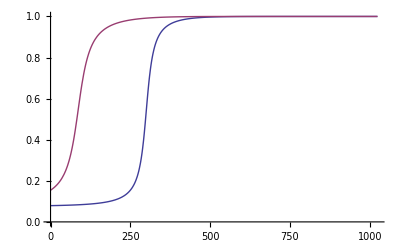

```mathematica
iifinal=TS1//.sol//.consts
Plot[{arctan,arctan2},{ii,0,iifinal}]
```

1a 1b 2a 2b finala finalb

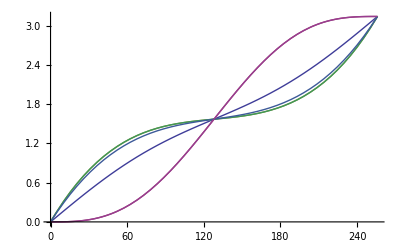

1a 1b finala finalb

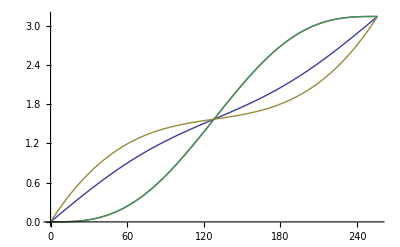

3a 3b

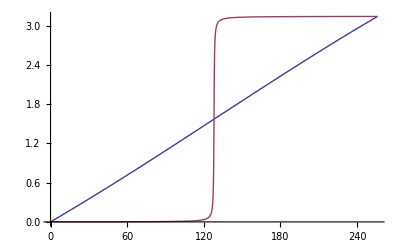

finala finalb

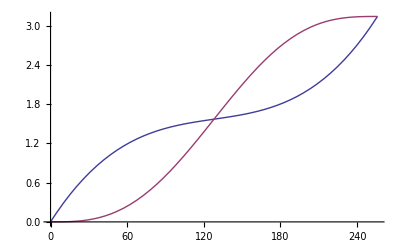

finala finalb theta3b

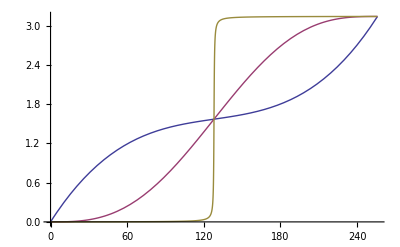

```mathematica
Clear[theta1plota,theta1plotb,theta2plota,theta2plotb]
theta1plota=theta1//.{ii->0}//.sol//.consts;
theta1plotb=theta1//.{ii->TS1}//.sol//.consts;
theta2plota=theta2//.{ii->0}//.sol//.consts;
theta2plotb=theta2//.{ii->TS1}//.sol//.consts;

theta3plota=theta3//.{ii->0}//.sol//.consts;
theta3plotb=theta3//.{ii->TS1}//.sol//.consts;

thetafinalplota=thetafinal//.{ii->0}//.sol//.consts;
thetafinalplotb=thetafinal//.{ii->TS1}//.sol//.consts;

Print["1a 1b 2a 2b finala finalb"];
Plot[{theta1plota,theta1plotb,theta2plota,theta2plotb,thetafinalplota,thetafinalplotb},{j,0,N2}]
Print["1a 1b finala finalb"];
Plot[{theta1plota,theta1plotb,thetafinalplota,thetafinalplotb},{j,0,N2}]
Print["3a 3b"];
Plot[{theta3plota,theta3plotb},{j,0,N2}]
Print["finala finalb"];
Plot[{thetafinalplota,thetafinalplotb},{j,0,N2}]
Print["finala finalb theta3b"];
Plot[{thetafinalplota,thetafinalplotb,theta3plotb},{j,0,N2}]
```

1024

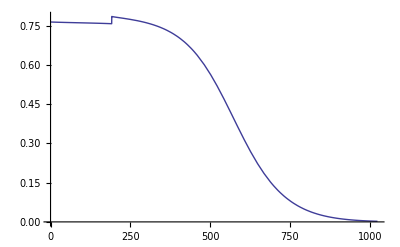

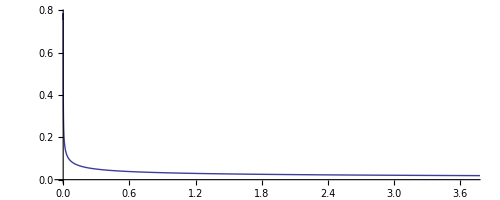

```mathematica
mytheta3=theta3//.{j->N2/4};
iifinal=TS1//.sol//.consts
Plot[mytheta3,{ii,0,iifinal}]
ParametricPlot[{myr,mytheta3},{ii,0,iifinal}]
```

```mathematica
(* Check how many angular cells expected in jet near BH *)
```

```mathematica
thetafinal//.{ii->0}//.sol//.consts//.{j->N2/8}
thetabhjet=thetafinal//.{ii->0}//.sol//.consts//.{j->N2/6}
diskcorona=0.3*2
(* diff should be roughly 0 to have jet, corona, and disk resolved with about 1/3 each of angular grid *)
diff=Pi-(diskcorona+thetabhjet)*2
```

0.781039

0.963645

0.6

0.014303

```mathematica
(* now do x3 grid *)
```

```mathematica
N3=64
sx3=0
ex3=1
dx3=(ex3-sx3)/N3
x3=sx3+k*dx3
phi=2*Pi*x3
```

64

0

1

1/64

k/64

(k π)/32

```mathematica
x1high=N[r//.{ii->0,j->0,k->0}/.consts//.sol]
x1low=N[r//.{ii->-1,j->0,k->0}/.consts//.sol]

x2high=N[(r*theta2)//.{ii->0,j->N2/2,k->0}//.consts//.sol]
x2low=N[(r*theta2)//.{ii->0,j->N2/2-1,k->0}//.consts//.sol]

x3high=N[(r*Sin[theta2]*phi)//.{ii->0,j->1/2,k->1}//.consts//.sol]
x3low=N[(r*Sin[theta2]*phi)//.{ii->0,j->1/2,k->0}//.consts//.sol]

Print["dts"];
poledt1=x1high-x1low
poledt2=x2high-x2low
poledt3=x3high-x3low
```

1.2

1.17033

1.88496

1.88275

0.00194447

0.

dts

0.0296669

0.0022097

0.00194447

```mathematica
myj=1;
x2high=N[(r*theta2)//.{ii->0,j->myj,k->0}//.consts//.sol]
x2low=N[(r*theta2)//.{ii->0,j->myj-1,k->0}//.consts//.sol];
diffx2=(x2high-x2low)
unihigh=N[(r*(Pi/N2*j))//.{ii->0,j->myj,k->0}//.consts//.sol]
unilow=N[(r*(Pi/N2*j))//.{ii->0,j->myj-1,k->0}//.consts//.sol];
diffunix2=(unihigh-unilow)
badness=diffx2/diffunix2
```

0.0394682

0.0394682

0.0147262

0.0147262

2.68013

```mathematica
(* flow at equator is about 5X less expensive *)
poledt2*5
```

0.0110485

```mathematica
cour=0.8
limitingdt=poledt2*5*cour
```

0.8

0.00883879

```mathematica
(* get res up to when switch on grid section: t_transition=3000 *)
(* Ensure set t_transition to 3000 instead of 3500 ! *)
sectionN1=515
r//.{ii->sectionN1}//.consts//.sol
```

515

3036.73

```mathematica
(* lone went to tf=3300 *)
lonerunsteps=8.19*10^5
loneres=256*128*32
costlone=loneres*lonerunsteps
```

819000.

1048576

8.58784×10^11

```mathematica
totaltime=5*10^3
totalsteps=totaltime/limitingdt
totalsteps/lonerunsteps
newres=sectionN1*N2*N3//.consts
newcost=newres*totalsteps
Print["RatCost"];
newcost/costlone
```

5000

565689.

0.690706

8437760

4.77314×10^12

RatCost

5.55803

```mathematica
(* TIMEORDER==2 instead of ==4 *)
(* Also, consider turning off DISS and LUM stuff *)
newperfimprovement=2
newSUs=newcost/costlone*127000/2
```

2

352935.

```mathematica
(* lonestar speed *)
zcps=564524
zcpspercpu=zcps/256.0
```

564524

2205.17

```mathematica
(* for aspect ratio issue *)
```

```mathematica
myi=70
x1high=N[r//.{ii->myi,j->0,k->0}/.consts//.sol]
x1low=N[r//.{ii->myi-1,j->0,k->0}/.consts//.sol]

x2high=N[(r*theta2)//.{ii->0,j->N2/2,k->0}//.consts//.sol]
x2low=N[(r*theta2)//.{ii->0,j->N2/2-1,k->0}//.consts//.sol]

x3high=N[(r*Sin[theta2]*phi)//.{ii->0,j->1/2,k->1}//.consts//.sol]
x3low=N[(r*Sin[theta2]*phi)//.{ii->0,j->1/2,k->0}//.consts//.sol]

Print["dts"];
poledt1=x1high-x1low
poledt2=x2high-x2low
poledt3=x3high-x3low
```

70

4.20063

4.14098

1.88496

1.88275

0.00194447

0.

dts

0.059658

0.0022097

0.00194447